```mathematica
(1/h^2)Integrate[2*Pi*Exp[-(β/(2*II))*(pθ^2+pϕ^2/Sin[θ]^2)+β*Ef*μ*Cos[θ]],{θ,0,Pi},{pθ,-Infinity,Infinity},{pϕ,-Infinity,Infinity}]
```

(8 II π^2 Sinh[Ef β μ])/(Ef h^2 β^2 μ)

```mathematica
(1/((8 II π^2 Sinh[Ef β μ])/(Ef h^2 β^2 μ)))(1/h^2)Integrate[(μ*Cos[θ])*2*Pi*Exp[-(β/(2*II))*(pθ^2+pϕ^2/Sin[θ]^2)+β*Ef*μ*Cos[θ]],{θ,0,Pi},{pθ,-Infinity,Infinity},{pϕ,-Infinity,Infinity}]
```

(Csch[Ef β μ] (Ef β μ Cosh[Ef β μ]-Sinh[Ef β μ]))/(Ef β)

```mathematica
(Csch[Ef β μ] (Ef β μ Cosh[Ef β μ]-Sinh[Ef β μ]))/(Ef β)//FullSimplify
```

-1/(Ef β)+μ Coth[Ef β μ]

```mathematica
D[-1/(Ef β)+μ Coth[Ef β μ],Ef]//FullSimplify
```

1/(Ef^2 β)-β μ^2 Csch[Ef β μ]^2

```mathematica
Limit[1/(Ef^2 β)-β μ^2 Csch[Ef β μ]^2,Ef->0]
```

(β μ^2)/3

```mathematica
-D[Log[(8 II π^2 Sinh[Ef β μ])/(Ef h^2 β^2 μ)],β]//FullSimplify
```

2/β-Ef μ Coth[Ef β μ]

```mathematica
D[2k*T-Ef μ Coth[Ef *μ/(k*T)],T]//FullSimplify
```

2 k-(Ef^2 μ^2 Csch[(Ef μ)/(k T)]^2)/(k T^2)

```mathematica
Limit[2 k-(Ef^2 μ^2 Csch[(Ef μ)/(k T)]^2)/(k T^2),T->0]
```

ConditionalExpression[2 k, Ef k μ>0]

```mathematica
Limit[2 k-(Ef^2 μ^2 Csch[(Ef μ)/(k T)]^2)/(k T^2),T->Infinity]
```

k

General::munfl: Csch[8158.51] is too small to represent as a normalized machine number; precision may be lost.

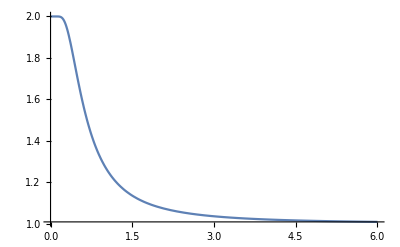

```mathematica
Plot[2-Csch[1/T]^2/T^2,{T,0,6},PlotRange->Full]
```